```mathematica
ClearAll["Global`*"];
Fg=m*g; (*Gravitational Force*)
Fc=m*ω^2*r; (*Centrifugal Force*)
Fs[x_,t_]:=(6*π*μ*d)*x'[t]; (*Stokes Law Drag Force*)
θ=π/4; (*Standard Angle of fixed rotor centrifuges*)
F=(Fg+Fc)*Cos[θ];
termxsol=DSolve[{F==Fs[x,t],x[0]==0},x[t],t]; (*Terminal Velocity Solution*)
xterm[t_] = FullSimplify[x[t]/.termxsol][[1]] ;
vterm=FullSimplify[D[xterm[t],t]](*Terminal Velocity*)
```

(m (g+r ω^2))/(6 √2 d π μ)

```mathematica
RPM=2000(*(360 degrees)/(60 s)*);nc=50(*#cells*);
r=0.159 (*Approximate big centrifuge radius in m*);g=9.81 (*Gravity m/s^2*);
d=nc*0.87*10^-6;(*diameter in m. cell diameter ~ 0.87um, (1m)/(10^6 um)*)
m=nc*150*10^-18;(*mass in kg. cell mass ~ 150fg, (1fg)/(10^18 kg)*)
ω=RPM*360/60*π/180;(*angular velocity in 1/s. degrees*π/180^o=radians, 1RPM =360^o per minute*)
μ=0.001; (*Viscocity of water Pa*s *)
```

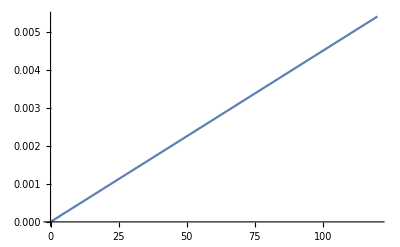

```mathematica
Plot[xterm[t],{t,0,120}]
```